```mathematica
(* IMPORT MODULES *)
SetDirectory[NotebookDirectory[]];
NotebookEvaluate["modules/oscillator_bracket.nb"];
NotebookEvaluate["modules/mews_and_alphas.nb"];
NotebookEvaluate["modules/operators.nb"];
NotebookEvaluate["modules/hamiltonian.nb"];
NotebookEvaluate["modules/silvestre_parameters.nb"];
NotebookEvaluate["modules/golden_search.nb"];
On[Assert]
```

```mathematica
data={};
For[g=1,g≤5,g++,
Print[g];
ClearAll[J,P,Isospin,γMax,Λ,m1,m2,m3,projector,project,size,firstNonZero];
(* INITIALISE HYPERPARAMETERS AND OBTAIN LOWEST LYING STATE *)
(**** !!!TUNABLE PARAMETERS!!! ****)
(**** !!!TUNABLE PARAMETERS!!! ****)
J=1/2;(* Total angular momentum J = Λ + S *)
P=+1;(* Parity P=(-1)^(Subscript[l, ρ]+Subscript[l, λ]) *)
Isospin=0;(* Isospin *)
γMax=g*2;(* Maximum energy of considered basis states (2n+l+2N+L), use this to control Subscript[N, Q] *)
Λ=0;(* Total orbital angular momentum Λ = Subscript[l, ρ] + Subscript[l, λ] *)
m1=uq;(* mass of quark 1 *)
m2=sq;(* mass of quark 2 *)
m3=cq;(* mass of quark 3 *)
(**** !!!END OF TUNABLE PARAMETERS!!! ****)
(**** !!!END OF TUNABLE PARAMETERS!!! ****)

(* Choose to project depending if m1=m2 or m1≠m2, True and False, respectively *)
If[m1==m2,project=True,project=False];

(* Obtain projector matrix *)
projector=Projector[J,P,Λ,γMax,Isospin];

(* Calculate generalised transformation matrices *)
{t1time,t1}=Timing[tMatrix[J,P,Λ,γMax,m1,m2,m3,1]];
Print["Time taken to compute t1: ",t1time];
{t2time,t2}=Timing[tMatrix[J,P,Λ,γMax,m1,m2,m3,2]];
Print["Time taken to compute t2: ",t2time];

(* Obtain size of basis from size of talmi matrices (Subscript[N, Q]) *)
size=Dimensions[t1][[1]];

(* If projector has been applied, find position of first non-zero eigenvalue, if not applied then it's 1 *)
If[project==True,firstNonZero=size-Total[Diagonal[projector]]+1,firstNonZero=1];
{a,b}=goldenSearch[0.4,0.8,0.001];
min=(a+b)/2;
eigvalMin=eigVal[min];
eigvalError=eigVal[a];
error=eigvalError-eigvalMin;
AppendTo[data,{size,Around[eigvalMin,error]}]
]
```

1

Time taken to compute t1: 0.035483

Time taken to compute t2: 0.038399

2

Time taken to compute t1: 0.181792

Time taken to compute t2: 0.17855

3

Time taken to compute t1: 0.838932

Time taken to compute t2: 0.849801

4

Time taken to compute t1: 6.23731

Time taken to compute t2: 5.75527

5

Time taken to compute t1: 36.7257

Time taken to compute t2: 35.5745

```mathematica
data
```

{{8,2.4935332320},{20,2.47243774254},{40,2.4683479235817},{70,2.46535269711},{112,2.4645857189}}

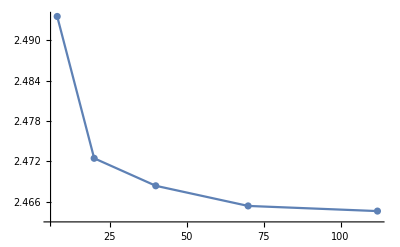

```mathematica
ListPlot[data,Joined->True,PlotMarkers->All,PlotRange->All]
```

```mathematica
data2=Table[{1/data[[i,1]],data[[i,2]][[1]]},{i,1,Length[data]}]
line=Fit[data2,{1,x},x]
parabola=Fit[data2,{1,x,x^2},x]
```

{{1/8,2.49353},{1/20,2.47244},{1/40,2.46835},{1/70,2.46535},{1/112,2.46459}}

2.46167+0.250419 x

2.4633+0.154731 x+0.695532 x^2

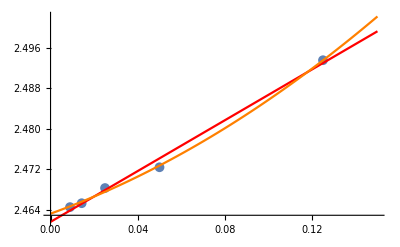

```mathematica
Show[ListPlot[data2,PlotMarkers->{Automatic, Medium}],Plot[line,{x,0,0.15},PlotStyle->Red],Plot[parabola,{x,0,0.15},PlotStyle->Orange],PlotRange->Full]
```

```mathematica
(* How to estimate error due to limited number of basis functions 
The error is dependent on the number of basis functions
If we knew the ground truth then the error would be the value we have minus the ground truth
how to define ground truth in a non-biased way? *)
```